# The Mobile 3rd Space

## Declare Base Constants

## Declare Thermal Resistances

## Equations

```mathematica
eqn2={C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Reff,C2 Twall'[t]==(Ttile[t]-Twall[t])/Reff-(Twall[t]-Tout)/R4,Ttile[0]==18.3,Twall[0]==18.3}
```

{C1 Ttile'[t]==Q-(Ttile[t]-Twall[t])/Reff,C2 Twall'[t]==(Ttile[t]-Twall[t])/Reff-(-Tout+Twall[t])/R4,Ttile[0]==18.3,Twall[0]==18.3}

```mathematica
sol=DSolveValue[eqn2,{Ttile[t],Twall[t]},t]
```

{(2. ⅇ^(-((1) t)/(2 C1 C2 R4 Reff^2)) (173+1. C1^2 C2 ⅇ^(1/1+1) R4 Reff^5 √(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2) Tout))/(Reff^2 (C1^2 R4^2+2. C1 C2 R4^2+C2^2 R4^2+2. C1^2 R4 Reff-2. C1 C2 R4 Reff+C1^2 Reff^2) (C1 R4 Reff+C2 R4 Reff+C1 1-1. √(-4 C1 C2 R4 Reff^3+((11)^2)) (C1 R4 Reff+C2 R4 Reff+C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2))),(2. ⅇ^-1 (1))/(Reff^2 (1) (1) (1))}
 |  |  |  |

```mathematica
tileTemp=sol⟦1⟧;
wallTemp=sol⟦2⟧;
airTemp[t_,Reff]=wallTemp+((tileTemp-wallTemp)(Reff-R1))/Reff
```

(2. ⅇ^(-((5+√(1+1)) t)/(2 C1 C2 R4 Reff^2)) (1))/(Reff^2 (C1^2 R4^2+2. C1 C2 R4^2+C2^2 R4^2+2. C1^2 R4 Reff-2. C1 C2 R4 Reff+C1^2 Reff^2) (C1 R4 Reff+C2 R4 Reff+C1 1-1. √(-4 C1 C2 R4 Reff^3+((11)^2)) (C1 R4 Reff+C2 R4 Reff+C1 Reff^2+√(-4 C1 C2 R4 Reff^3+(C1 R4 Reff+C2 R4 Reff+C1 Reff^2)^2)))+((-R1+Reff) (-(2. ⅇ^1 (1))/(Reff^2 2 (1))+1))/Reff
 |  |  |  |

## Calculate Thermal Resistances & Define Constants

```mathematica
r1=1/(70 14.8645);
r2=1/(70 71.3495);
r3=0.5/(0.02 71.3495);
r4=1/(13 71.3495)
Ref=r1+r2+r3
c1=4000 800;(*m1 C1*)
c2=200 100;(*m2 C2*)
tout=-3+6 Sin[(2 π t)/(24 60 60)]+(3 π)/4
qout=(-0.361 Cos[(t π)/(12 3600)]+0.2243 Cos[(t π)/(6 3600)]+0.2097) 
qin = 4.64515 qout
```

0.00107812

0.351549

-3+(3 π)/4+6 Sin[(π t)/43200]

0.2097-0.361 Cos[(π t)/43200]+0.2243 Cos[(π t)/21600]

4.64515 (0.2097-0.361 Cos[(π t)/43200]+0.2243 Cos[(π t)/21600])

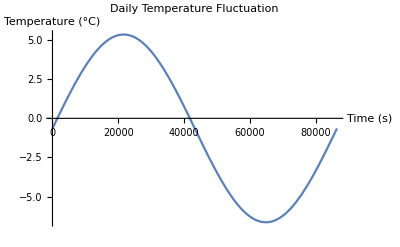

```mathematica
Plot[tout, {t, 0, 86400}, PlotLabel->"Daily Temperature Fluctuation",AxesLabel->{"Time (s)", "Temperature (°C)"}]
```

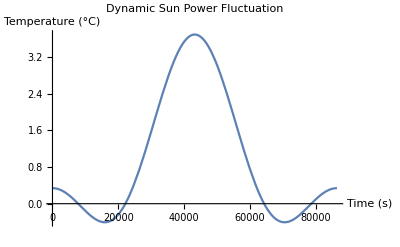

```mathematica
Plot[qin, {t, 0, 86400}, PlotLabel->"Dynamic Sun Power Fluctuation",AxesLabel->{"Time (s)", "Temperature (°C)"}]
```

## Plotting

### Result with Constant Flux and Exterior Temperature

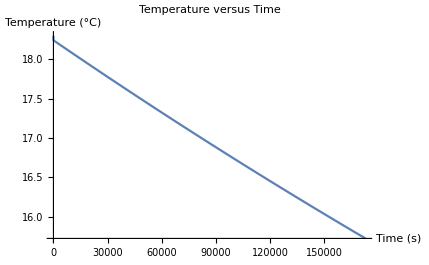

```mathematica
Plot[airTemp[t,Reff]/.{R1->N[r1],R4->N[r4],Reff->N[Ref],C1->N[c1],C2->N[c2],C3->9,Q->10,Tout->-3,C[1]->4},{t,0,86400*2}, PlotLabel->"Temperature versus Time",AxesLabel->{"Time (s)","Temperature (°C)"}]
```

### Result with Variable Flux and Exterior Temperature

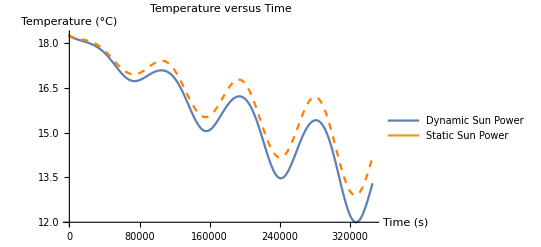

```mathematica
days=4;
Legended[Show[{Plot[airTemp[t,Reff]/.{R1->N[r1],R4->N[r4],Reff->N[Ref],C1->N[c1],C2->N[c2],Q->qin,Tout-> tout},{t,0,86400*days}, PlotLabel->"Temperature versus Time",AxesLabel->{"Time (s)","Temperature (°C)"}],Plot[airTemp[t,Reff]/.{R1->N[r1],R4->N[r4],Reff->N[Ref],C1->N[c1],C2->N[c2],Q->10,Tout-> tout},{t,0,86400*days}, PlotLabel->"Temperature versus Time",AxesLabel->{"Time (s)","Temperature (°C)"},PlotStyle->{Orange, Dashed, Thick}]}], LineLegend[ColorData[97]/@{1,2},{"Dynamic Sun Power","Static Sun Power"}]]
```

### Modeling Improvements

Improve parameter accuracy

Determine initial values